```mathematica
f[t_]=48*t^2*(1-t^2)^2-8*(1-t^2)^3
```

48 t^2 (1-t^2)^2-8 (1-t^2)^3

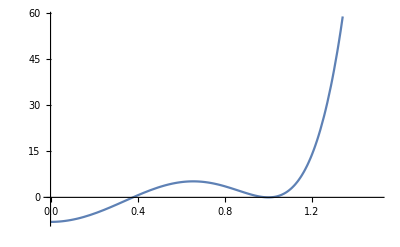

```mathematica
Plot[f[t],{t,0,1.5}]
```

```mathematica
f[1]
```

0

```mathematica
FourierTransform[f[t],t,ω]
```

-8 √(2 π) DiracDelta[ω]-72 √(2 π) DiracDelta''[ω]-120 √(2 π) DiracDelta^(4)[ω]-56 √(2 π) DiracDelta^(6)[ω]

```mathematica
g[t_]=Piecewise[{{f[t],Abs[t]≤1},{0,Abs[t]>1}}]
```

Piecewise[{{48 t^2 (1-t^2)^2-8 (1-t^2)^3, Abs[t]≤1}, {0, True}}]

```mathematica
FourierTransform[g[t],t,ω]
```

-(384 √(2/π) (5 ω (-21+2 ω^2) Cos[ω]+(105-45 ω^2+ω^4) Sin[ω]))/ω^7

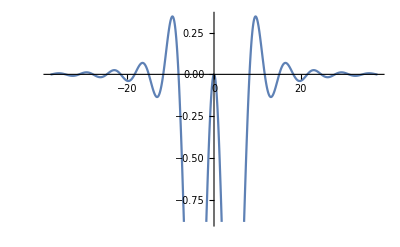

```mathematica
Plot[-(384 √(2/π) (5 ω (-21+2 ω^2) Cos[ω]+(105-45 ω^2+ω^4) Sin[ω]))/ω^7,{ω,-37.69911184307752,37.69911184307752}]
```